## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Column@Table[ToString@i<>".  ",{i,21}];
```

```mathematica
niceForm[{x_,y_}]:=TraditionalForm[x î + y ĵ]
niceForm[{x_,y_,z_}] := TraditionalForm[x î + y ĵ+z k̂]
```

```mathematica
ihat:={0,1}; ihat3:={1,0,0};
jhat:={1,0}; jhat3:={0,1,0};
khat3:={0,0,1};
```

## 3

### Sliding

```mathematica
es={1/Sqrt[5] FT==FN μs,
2/Sqrt[5]FT+FN==m g}
```

{FT/(√5)==FN μs,FN+(2 FT)/(√5)==g m}

```mathematica
Eliminate[es,FN]
```

√5 FT (1+2 μs)==5 g m μs

```mathematica
Solve[√5 FT (1+2 μs)==5 g m μs&&m∈Integers,{FT}]
```

{{FT→ConditionalExpression[(√5 g m μs)/(1+2 μs),m∈Integers]}}

```mathematica
e2=FullSimplify[(√5 g m μs)/(1+2 μs)]
```

(√5 g m μs)/(1+2 μs)

```mathematica
Limit[(√5 g m μs)/(1+2 μs),μs->Infinity]
```

1/2 √5 g m

```mathematica
%/(m g/Sqrt[5])
```

5/2

```mathematica
e1=m g/Sqrt[5]
```

(g m)/(√5)

```mathematica
Plot[{(√5 g m μs)/(1+2 μs)}
```

```mathematica
Assuming[{g>0,m>0},FullSimplify[e1<e2]]
```

μs+6 μs^2>1

```mathematica
5/2*e2
```

(5 √5 g m μs)/(2 (1+2 μs))

## 4

### c

```mathematica
FN1=m1 g Cos[θ];
FF1=FN1*μk1;
Fg = m2 g
```

g m2

```mathematica
FNy=Fg+FN1 Cos[θ]+FF1 Sin[θ]
FNx=-(FN1 Sin[θ]-FF1 Cos[θ])
```

g m2+g m1 Cos[θ]^2+g m1 μk1 Cos[θ] Sin[θ]

g m1 μk1 Cos[θ]^2-g m1 Cos[θ] Sin[θ]

```mathematica
Simplify@Assuming[{θ∈Reals,g>0,m1>0,m2>0,μk1>0},Norm[{FNx,FNy}]]
```

√(Abs[g m1 Cos[θ] (μk1 Cos[θ]-Sin[θ])]^2+Abs[g (m2+m1 Cos[θ]^2+m1 μk1 Cos[θ] Sin[θ])]^2)

## 5: Masses on springs

#### Problem analysis

Let k be the spring constant, and the bar be massless.

```mathematica
l0=Sqrt[Quantity[1.5, "Meters"]^2+Quantity[2, "Meters"]^2]
l=Sqrt[Quantity[2, "Meters"]^2+(Quantity[1.5, "Meters"]+d)^2]
```

2.5 m

√((d+1.5 m)^2+4 m^2)

```mathematica
F=k(l-l0);
Subscript[F, y]=F(Quantity[1.5, "Meters"]+d)/l;
```

#### Total force (weight) of one block

```mathematica
Subscript[F, y]/.d->Quantity[2, "Meters"]
```

k (1.32939 m)

## 6: Wing

### (a)

#### Find length of wing

```mathematica
L[x_]=200 Sqrt[1-x^2/17];
Solve[L[x]==0,x]
```

{{x→-√17},{x→√17}}

#### Set up forces and radii

```mathematica
Fg={0,-1600,0}LinguisticAssistant;
Rg = {Sqrt[17]/2,0,0}LinguisticAssistant;
Flift={0,50 Sqrt[17] Pi,0}LinguisticAssistant;
Rlift={4 Sqrt[17] / (3 Pi),0,0}LinguisticAssistant;
```

#### Solve newton’s 2nd law equations

```mathematica
N@Solve[{Flift+Fg+{0,Freact,0}==0,{0,0,Treact}+Rg×Fg+Rlift×Flift==0},{Freact,Treact}]
```

{{Freact→952.344 N,Treact→2165.15 J}}

### (b)

#### Problem analysis

Basic assumptions: There are no structural loads being carried as torques in the joints...
The strut is mounted d meters below the wing mount

#### Forces

```mathematica
Freact={Freactx,Freacty,0};
Fstrut=Fstrutl*-Normalize[{2,d,0}];
Rstrut={2 Quantity[, "Meters"],0,0};
```

#### General Solution

```mathematica
sol=Solve[{Flift+Fg+Freact+Fstrut==0,Rstrut×Fstrut+Rg×Fg+Rlift×Flift==0},{Freactx,Freacty,Fstrutl}][[1]];
```

Final result:

```mathematica
N@niceForm[Freact/.sol]
N@(Fstrutl/.sol)
```

(î (-2165.15 N))/d+ĵ (-130.232 N)

(√(4.+Abs[d]^2) (-1082.58 N))/d

#### Specific solution

Assuming that d=1 "m" yields the following specific result:

```mathematica
N@niceForm[Freact/.sol/.d->1]
N@(Fstrutl/.sol/.d->1)
```

î (-2165.15 N)+ĵ (-130.232 N)

-2420.71 N

## 7: Floating block

#### Problem Analysis

This problem has the trivial case, solved here, where the block is a cube. Another (pair of) solutions exist, but calculating them is an exercise for another day.

#### Forces

```mathematica
Flead={0,-(m-(m/Entity["Element","Lead"][EntityProperty["Element","Density"]])*Entity["Chemical","Water"][EntityProperty["Chemical","Density"]])*Quantity[, "StandardAccelerationOfGravity"],0};
Fg={0,-(Quantity[10, "Centimeters"]*Quantity[10, "Centimeters"]*d*Quantity[20, ("Kilograms")/("Meters")^3]*Quantity[, "StandardAccelerationOfGravity"]),0};
Fbuoyancy={0,(Quantity[10, "Centimeters"]*Quantity[10, "Centimeters"]*d*Entity["Chemical","Water"][EntityProperty["Chemical","Density"]]/2*Quantity[, "StandardAccelerationOfGravity"]),0};
```

#### Solve Equations of Motion

```mathematica
Solve[(Flead+Fg+Fbuoyancy==0)/.d->Quantity[10, "Centimeters"],{m}]
```

{{m→526.422 g}}

## 8: Beam

#### Problem Analysis

Definitions:
- Origin is at left support
- x right, y up

#### Calculating equivalent forces

```mathematica
Module[{f},
f[x_]:={0,-Piecewise[{{200,x<4},{200(7-x)/3,x≥4}}],0};
Fload=Integrate[f[x],{x,-3,7}];
Rload=Integrate[Norm@f[x]{ x,0,0},{x,-3,7}]/Norm[Fload];
]
```

#### Setting up forces

```mathematica
Fpin={0,Fpiny,0};
Froller={0,Frollery,0};
Rroller={7,0,0};
```

```mathematica
Fload+Fpin+Froller
```

{0,-1700+Fpiny+Frollery,0}

```mathematica
Rload×Fload+Rroller×Froller
```

{0,0,-2200+7 Frollery}

#### Solving equations of motion

```mathematica
N@Solve[{Fload+Fpin+Froller=={0,0,0},Rload×Fload+Rroller×Froller=={0,0,0}},{Fpiny,Frollery}]
```

{{Fpiny→1385.71,Frollery→314.286}}

## 9: Three blocks

#### Problem analysis

This problem is statically indeterminate because for a given load, the force can be distributed in many ways between the tension in the rope and the friction on the base. For the remainder of this problem, I assume those indeterminisms are resolved in the most favorable way for the blocks not slipping.

#### Figure out forces perpendicular to the force F

```mathematica
Clear[θ,F]
```

```mathematica
g=Quantity[, "StandardAccelerationOfGravity"];
Fn12[θ_]:=Quantity[30, "Kilograms"]g Cos[θ];
Fn23[θ_]:=Fn12[θ]+Quantity[50, "Kilograms"]g Cos[θ];
Fn3g[θ_]:=Fn23[θ]+Quantity[40, "Kilograms"]g Cos[θ];
```

#### Consider the system containing only block 1

```mathematica
block1slips[θ_,F_]:=-Quantity[30, "Kilograms"]g Sin[θ]≥0.3*Fn12[θ]
```

#### Consider the system containing only block 2

```mathematica
block2slips[θ_,F_]:=F+Quantity[50, "Kilograms"]g Sin[θ]≥0.3*Fn12[θ]+0.4*Fn23[θ]
```

#### Consider the system containing blocks 2 and 3

```mathematica
blocks23slip[θ_,F_]:=F+Quantity[90, "Kilograms"]g Sin[θ]+Quantity[50, "Kilograms"]g Sin[θ]≥0.3*Fn12[θ]+0.45*Fn3g[θ]
```

#### Plot the results

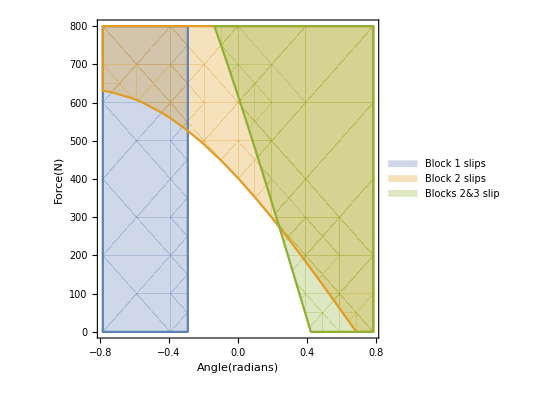

```mathematica
RegionPlot[Evaluate@{block1slips[θ,F],block2slips[θ,F],blocks23slip[θ,F]},{θ,-Pi/4,Pi/4},{F,0,Quantity[800, "Newtons"]},PlotPoints->5,PlotLegends->{"Block 1 slips","Block 2 slips", "Blocks 2&3 slip"},AxesLabel->{"Angle(radians)","Force(N)"}]
```

To clarify how this graph works: Each region represents the set of conditions under which the specified sets of joints would be satisfied with yielding, under the most optimal of the available statically indeterminate load distributions. In particular, the lowest color for a given coordinate is always the first to occur.

## 10: Static Indeterminism

### 1. Parked car

Because there are an infinite number of ways the wheels could be applying force toward each other with the parking brakes on, it is indeterministic.

### 2. Problem 9

As touched on before, if the string is slightly streachier than the frictional joints (a detail that lives outside the model), it will absorb less load, and the converse is true also.